```mathematica
area[r_]:=N[π*r^2];
c[r_]:=N[2π*r];
ϵ=0.1;(*infinitesimal quantity*)
d[r_]:=r+ϵ;
stest[r_]:=c[r-ϵ]*ϵ;
```

```mathematica
Plot[{area[r],area[d[r]]},{r,0,5},Frame->True,Axes->True,AspectRatio->0.8,FrameStyle->Directive[Black,Thick],FrameLabel->{"r","Area_r"}]
```

```mathematica
area[d[4]]-area[4]
```

2.54469

```mathematica
stest[4]
```

2.45044

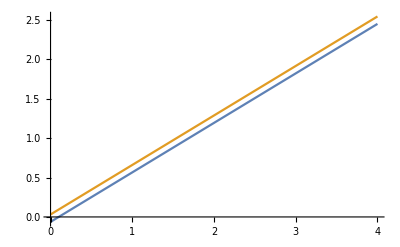

```mathematica
Plot[{stest[r],area[d[r]]-area[r]},{r,0,4}]
```